## Preamble

### Units and constants

```mathematica
$Assumptions={GeV>0};
Kg =N[ 5.6096 10^26]GeV; Gram = 10^-3 Kg;
Meter = N[1/(0.1973 10^-15)] GeV^-1;CentiMeter = 10^-2 Meter;
Second = N[299792458] Meter; Hz = Second^-1;
Hour = 3600 Second;Year = 365 24 Hour;
Kelvin = 8.6 10^-5 eV;
Joule = Kg Meter^2 Second^-2; erg = 10^-7 Joule; Watt = Joule Second^-1;
Newton = Kg Meter Second^-2;
Tesla =N[195] eV^2;Gauss=10^-4 Tesla;
ElectronCharge  = 0.303;
Volt = eV/ElectronCharge;
MProton = 0.938 GeV;
MElectron = 511.keV;
MMuon =105.6583745MeV;
MTau=1776.86MeV;
MPion=0.13957018GeV;
MQuarkUp = 2.01 MeV;
MQuarkDown = 4.79MeV;
MZboson=91.1876GeV;MWboson=80.379 GeV;MHiggs=125.18 GeV;
Coulomb = (5.28 10^-19)^-1;
MuNuclear = ElectronCharge/(2 MProton); MuBohr = ElectronCharge/(2MElectron); BohrRadius = 1/(AlphaEM MElectron);
Debye = 3.33564 10^-30 Coulomb Meter; Angstrom  =10^-10 Meter;
barn = 10^-28 Meter^2; fb = 10^-15 barn;
Ampere = Coulomb/Second; Ohm = Volt/Ampere; Farad = Coulomb/Volt; Henry = Joule/Ampere^2;
Subscript[G, F]=N[1.166 10^-5] GeV^-2;
AlphaEM = 1/137;
MPlanck = 1.2209×10^19 GeV; GN = MPlanck^-2;
mPlanck = MPlanck/√(8π);
meV = 10^-3 eV; eV = 10^-3 keV; keV =  10^-3 MeV; MeV= 10^-3 GeV;
Hubble0 = 67.8 10^3 Meter Second^-1 Mpc^-1; RhoCrit =(3 Hubble0^2)/(8π GN); hubble0 = Hubble0/(100 10^3 Meter Second^-1 Mpc^-1);
RhoCritOverhSq=1.05371 10^-5 GeV CentiMeter^-3;entropy0=Pi^4/(45*Zeta[3])(2+21/11)*410.7 CentiMeter^-3;
OmegaDM=0.12;
zeq = 3250;HubbleEq = Hubble0(1+zeq)^(3/2);aeq = N@(1/(1+zeq));
RhoDMU = 0.23 3/(8π)Hubble0^2 MPlanck^2;
RhoDMG = (0.4 GeV)/CentiMeter^3;
v0DM = 235 10^3 Meter Second^-1; σvDM = v0DM/√2;
kpc = 3261 Year; Mpc = 10^3 kpc;
pc = 10^-3 kpc;
AU = 150 10^6 10^3 Meter;
MSolar = 1.98 10^30 Kg;
MassEarth = 5.972 10^24 Kg;
MassMoon = 0.012300MassEarth;
MassDensityEarth = 5.59 Kg/(10CentiMeter)^3;
RadiusEarth = 6371 10^3 Meter;
NAvo = 6.022 10^23;
bar = 10^5 Newton Meter^-2;
Torr = 1/750.061683 bar;
nst = (1 bar)/(273.15Kelvin);
arcmin = (2π)/360 1/60;arcsec = (2π)/360 1/3600;mas = 10^-3 arcsec;muas = 10^-6 arcsec;
masy = 10^-3 arcsec Year^-1;muasy = 10^-6 arcsec Year^-1; muasyy = 10^-6 arcsec Year^-2;
Jy=10^-23 erg Second^-1 CentiMeter^-2 Hz^-1;
```

### Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$DataDir = "../data/";
$ListDir = "../lists/";
$FigDir = "../figs/";
```

### Plot options

```mathematica
fontsize=20;
plotstyle={FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle->{{Black,Black},{Black,Black}},(*PlotRange->All,*)Background->White,ImageSize->500,LabelStyle-> Directive[fontsize,Black,FontFamily->Times],FrameStyle-> Directive[fontsize,Black,FontFamily->"Times"(*Times*)],Frame->True,(*GridLines->Automatic,GridLinesStyle->Directive[Lighter[Gray,0.8],Thickness->0.001], *)Axes->False,AspectRatio->GoldenRatio^-1(*,PlotRangePadding->None*)};
plotstylelog={FrameTicksStyle->{{Black,Black},{Black,Black}},PlotRange->All,Background->White,ImageSize->500,GridLines->Automatic,LabelStyle-> Directive[fontsize,Black,FontFamily->Times],FrameStyle-> Directive[fontsize,Black,FontFamily->Times],Frame->True,GridLinesStyle->Directive[Lighter[Gray,0.8],Thickness->0.001], Axes->False,AspectRatio->GoldenRatio^-1};
```

## Photon to axion conversion

```mathematica
(* Defintion of ϕ[z] = Integrate[Δp[z]-Δa,{zz,zi,z}] *)
Ap[z]=(I a'[z]Exp[I ϕ[z]])/Δaγ[z];
```

```mathematica
D[(I a'[z]Exp[I ϕ[z]])/Δaγ[z],z]
```

-(ⅈ ⅇ^(ⅈ ϕ[z]) a'[z] Δaγ'[z])/Δaγ[z]^2-(ⅇ^(ⅈ ϕ[z]) a'[z] ϕ'[z])/Δaγ[z]+(ⅈ ⅇ^(ⅈ ϕ[z]) a''[z])/Δaγ[z]

```mathematica
Simplify[I (-(ⅈ ⅇ^(ⅈ ϕ[z]) a'[z] Δaγ'[z])/Δaγ[z]^2-(ⅇ^(ⅈ ϕ[z]) a'[z] ϕ'[z])/Δaγ[z]+(ⅈ ⅇ^(ⅈ ϕ[z]) a''[z])/Δaγ[z])==Δaγ[z] a[z]Exp[I ϕ[z]]]
```

a[z] Δaγ[z]^2+ⅈ a'[z] ϕ'[z]+a''[z]==(a'[z] Δaγ'[z])/Δaγ[z]

```mathematica
a[zt]+ⅈ a'[zt] ϕ'[zt]+a''[zt]==0
```

```mathematica
zeroD=Exp[-I ϕ[zt]/2]u[zt]
firstD=Simplify[D[Exp[-I ϕ[zt]/2]u[zt],zt]]
secondD=Simplify[D[Exp[-I ϕ[zt]/2]u[zt],{zt,2}]]
```

ⅇ^(-1/2 ⅈ ϕ[zt]) u[zt]

1/2 ⅇ^(-1/2 ⅈ ϕ[zt]) (2 u'[zt]-ⅈ u[zt] ϕ'[zt])

1/4 ⅇ^(-1/2 ⅈ ϕ[zt]) (-4 ⅈ u'[zt] ϕ'[zt]+4 u''[zt]-u[zt] (ϕ'[zt]^2+2 ⅈ ϕ''[zt]))

```mathematica
Simplify[zeroD+ⅈ firstD ϕ'[zt]+secondD==0]
```

4 u''[zt]+u[zt] (4+ϕ'[zt]^2-2 ⅈ ϕ''[zt])==0

```mathematica
((10^-12 eV)^2)/(4 10^-4 eV 10^-12 GeV^-1 10^-6 Gauss)
```

1.28205×10^8

```mathematica
((10^-12 eV)^2)/(4 10^-4 eV (10^-12 GeV^-1 10^-6 Gauss)^2 0.01Mpc)
```

4.20746×10^9

```mathematica
Δpfnc[zt_]:=(zt-3)^2;
ϕpfnc[zt_]:=2 (-3+zt);
ϕppfnc[zt_]:=2 ;
```

```mathematica
s=NDSolve[{y''[x]+ (ϕpfnc[x]-I ϕppfnc[x])y[x]==0,y[0]==1,y'[0]==0},y,{x,0,30}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
Evaluate[y[2]/.s]
```

{21.2553+27.9773 ⅈ}

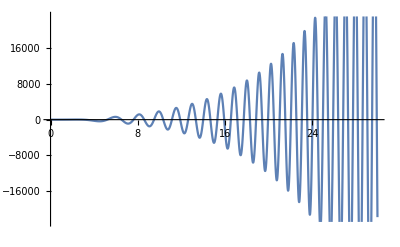

```mathematica
Plot[Evaluate[{Re[y[x]]}/.s],{x,0,30},PlotStyle->Automatic]
```

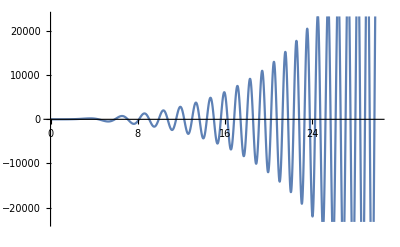

```mathematica
Plot[Evaluate[{Im[y[x]]}/.s],{x,0,30},PlotStyle->Automatic]
```

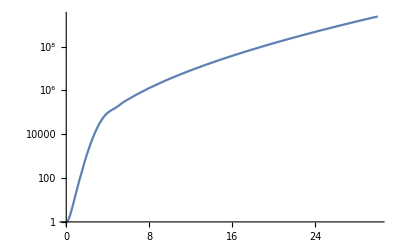

```mathematica
LogPlot[Evaluate[{Re[y[x]]^2+Im[y[x]]^2}/.s],{x,0,30},PlotStyle->Automatic]
```